```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/pp/v2/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

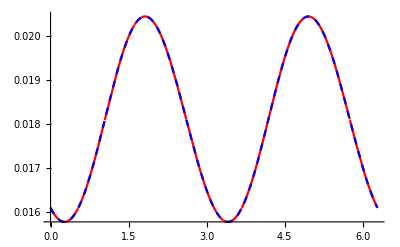

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression -(ⅈ (0.+0. ⅈ) ComplexInfinity)/(4 π) encountered.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 12; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ)+EulerGamma+-∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression Indeterminate should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

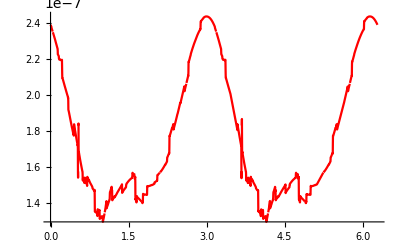

```mathematica
Plot[J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1,{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

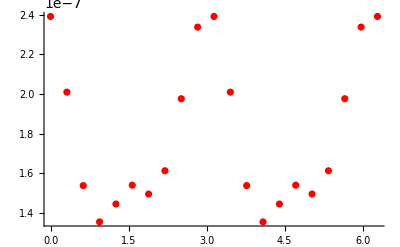

```mathematica
ListPlot[Table[{ϕ,J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]/J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]-1},{ϕ,0,2π,0.1π}],PlotStyle->{{Red},{Blue,Dashed}}]
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[bu+x1u,bu+x2u,x3u,x4u,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u,x2u,bu+x3u,bu+x4u,{kT,ϕ}],{ϕ,0,2π}]
]
```

## b = 1

### r = 0.1

```mathematica
v2kTr01={};
For[i=1,i≤120,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$128061620 near {ϕ$128061620} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$128113545 near {ϕ$128113545} = {5.08045}. NIntegrate obtained -4.84395×10^-16 and 2.90601×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$128203887 near {ϕ$128203887} = {4.20915}. NIntegrate obtained -4.10856×10^-18 and 3.96797×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kTr01
```

{{0.25,{-0.0157187,4.45577×10^-15}},{0.5,{-0.062827,-9.20926×10^-12}},{0.75,{-0.139328,-2.00755×10^-13}},{1.,{-0.240227,1.77613×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.75,{-0.591091,7.7825×10^-10}},{2.,{-0.677349,-1.10209×10^-13}},{2.25,{-0.726966,2.70404×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.75,{-0.719943,-4.26028×10^-14}},{3.,{-0.684442,-2.18537×10^-10}},{3.25,{-0.643735,-1.25544×10^-6}},{3.5,{-0.605698,-1.79259×10^-14}},{3.75,{-0.574323,-4.14661×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{5.,{-0.528467,2.38943×10^-14}},{5.25,{-0.536388,2.11343×10^-8}},{5.5,{-0.548162,1.11488×10^-14}},{5.75,{-0.563122,5.39756×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.25,{-0.600009,4.35246×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.75,{-0.641511,4.96233×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.25,{-0.681019,1.36393×10^-14}},{7.5,{-0.697642,-1.31854×10^-14}},{7.75,{-0.710858,-2.09258×10^-14}},{8.,{-0.719767,-1.24401×10^-15}},{8.25,{-0.723653,-1.38475×10^-14}},{8.5,{-0.722076,2.28796×10^-14}},{8.75,{-0.714966,2.02798×10^-6}},{9.,{-0.702631,1.28915×10^-7}},{9.25,{-0.685778,7.09638×10^-15}},{9.5,{-0.665429,-8.58115×10^-8}},{9.75,{-0.642763,1.7996×10^-9}},{10.,{-0.619111,7.59579×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.5,{-0.573702,-4.43718×10^-7}},{10.75,{-0.553992,4.0396×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.25,{-0.523987,2.72869×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{13.,{-0.524609,2.11315×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.5,{-0.542427,-5.10646×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{14.,{-0.558401,-5.68867×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.25,{-0.560756,1.25152×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.75,{-0.543873,-9.58429×10^-15}},{16.,{-0.532927,-3.87923×10^-15}},{16.25,{-0.521115,-6.79951×10^-15}},{16.5,{-0.509113,8.01134×10^-14}},{16.75,{-0.497507,-3.77202×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.25,{-0.47777,3.74349×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{18.,{-0.461929,-4.03007×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.5,{-0.461883,-2.08973×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{19.,{-0.46897,-3.82806×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.75,{-0.4867,-1.72874×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.25,{-0.49782,-7.17622×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.75,{-0.504133,-4.93938×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.75,{-0.49478,8.20305×10^-15}},{22.,{-0.488089,2.61801×10^-8}},{22.25,{-0.480229,-5.37731×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.75,{-0.46269,-7.61967×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.25,{-0.445733,9.61877×10^-8}},{23.5,{-0.438406,-6.45213×10^-8}},{23.75,{-0.432338,-2.3747×10^-13}},{24.,{-0.427743,-9.23792×10^-8}},{24.25,{-0.424703,4.40993×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.75,{-0.423365,3.09228×10^-7}},{25.,{-0.42485,-3.94661×10^-14}},{25.25,{-0.427551,5.47303×10^-17}},{25.5,{-0.431117,-7.25639×10^-15}},{25.75,{-0.435291,-2.88181×10^-14}},{26.,{-0.439572,-1.21974×10^-14}},{26.25,{-0.44375,-1.4636×10^-8}},{26.5,{-0.447275,-1.24115×10^-6}},{26.75,{-0.449846,-2.78558×10^-15}},{27.,{-0.45121,4.63195×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.25,{-0.435217,1.81927×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{29.,{-0.411968,-2.64344×10^-7}},{29.25,{-0.40379,-6.46534×10^-9}},{29.5,{-0.396003,3.62264×10^-7}},{29.75,{-0.388929,2.53649×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

```mathematica
v2kTr01={};
For[i=1,i≤240,i++,
x1u=0.05{Cos[π/2],Sin[π/2]};
x3u=0.05{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr01,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr01
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192131759 near {ϕ$192131759} = {5.71858}. NIntegrate obtained 9.12678×10^-18 and 7.00796×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192194508 near {ϕ$192194508} = {0.944835}. NIntegrate obtained 1.05313×10^-18 and 7.75677×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$192246433 near {ϕ$192246433} = {1.90204}. NIntegrate obtained -3.23138×10^-18 and 3.01729×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{-0.00391806,9.24485×10^-15}},{0.25,{-0.0157187,4.45577×10^-15}},{0.375,{-0.0354044,-3.24943×10^-14}},{0.5,{-0.062827,-9.20926×10^-12}},{0.625,{-0.0976425,1.13234×10^-11}},{0.75,{-0.139328,-2.00755×10^-13}},{0.875,{-0.18716,3.65879×10^-14}},{1.,{-0.240227,1.77613×10^-12}},{1.125,{-0.297416,1.63936×10^-12}},{1.25,{-0.35739,-2.93311×10^-14}},{1.375,{-0.418602,5.56247×10^-14}},{1.5,{-0.479261,2.14831×10^-11}},{1.625,{-0.537441,-4.3328×10^-12}},{1.75,{-0.591091,7.7825×10^-10}},{1.875,{-0.638266,-1.63048×10^-13}},{2.,{-0.677349,-1.10209×10^-13}},{2.125,{-0.707092,-2.29806×10^-14}},{2.25,{-0.726966,2.70404×10^-14}},{2.375,{-0.737136,6.27389×10^-14}},{2.5,{-0.738423,1.05985×10^-13}},{2.625,{-0.732143,6.6596×10^-14}},{2.75,{-0.719943,-4.26028×10^-14}},{2.875,{-0.703491,-5.24726×10^-15}},{3.,{-0.684442,-2.18537×10^-10}},{3.125,{-0.664112,2.06704×10^-7}},{3.25,{-0.643735,-1.25544×10^-6}},{3.375,{-0.624029,2.33796×10^-9}},{3.5,{-0.605698,-1.79259×10^-14}},{3.625,{-0.589021,3.152×10^-15}},{3.75,{-0.574323,-4.14661×10^-14}},{3.875,{-0.561591,3.64852×10^-14}},{4.,{-0.550945,1.79277×10^-14}},{4.125,{-0.542226,1.09035×10^-14}},{4.25,{-0.535463,1.70267×10^-14}},{4.375,{-0.530442,4.75911×10^-14}},{4.5,{-0.527157,3.12895×10^-14}},{4.625,{-0.525386,3.59845×10^-14}},{4.75,{-0.525121,-2.42844×10^-15}},{4.875,{-0.526151,2.7405×10^-14}},{5.,{-0.528467,2.38943×10^-14}},{5.125,{-0.531883,1.14919×10^-15}},{5.25,{-0.536388,2.11343×10^-8}},{5.375,{-0.54182,1.20107×10^-14}},{5.5,{-0.548162,1.11488×10^-14}},{5.625,{-0.555274,-8.20707×10^-15}},{5.75,{-0.563122,5.39756×10^-15}},{5.875,{-0.571586,7.41448×10^-15}},{6.,{-0.580625,4.77842×10^-15}},{6.125,{-0.590118,1.36165×10^-14}},{6.25,{-0.600009,4.35246×10^-15}},{6.375,{-0.610183,6.64694×10^-15}},{6.5,{-0.620565,-3.95808×10^-15}},{6.625,{-0.631035,-0.0000186778}},{6.75,{-0.641511,4.96233×10^-15}},{6.875,{-0.651861,2.55459×10^-15}},{7.,{-0.661978,1.08362×10^-14}},{7.125,{-0.671738,-2.92902×10^-15}},{7.25,{-0.681019,1.36393×10^-14}},{7.375,{-0.689696,6.94386×10^-15}},{7.5,{-0.697642,-1.31854×10^-14}},{7.625,{-0.704735,5.44791×10^-15}},{7.75,{-0.710858,-2.09258×10^-14}},{7.875,{-0.715901,-9.91784×10^-15}},{8.,{-0.719767,-1.24401×10^-15}},{8.125,{-0.722373,1.05616×10^-14}},{8.25,{-0.723653,-1.38475×10^-14}},{8.375,{-0.723562,-1.03857×10^-6}},{8.5,{-0.722076,2.28796×10^-14}},{8.625,{-0.719204,-8.35843×10^-15}},{8.75,{-0.714966,2.02798×10^-6}},{8.875,{-0.709417,-5.23131×10^-15}},{9.,{-0.702631,1.28915×10^-7}},{9.125,{-0.694717,-2.14784×10^-14}},{9.25,{-0.685778,7.09638×10^-15}},{9.375,{-0.676018,5.70954×10^-10}},{9.5,{-0.665429,-8.58115×10^-8}},{9.625,{-0.65429,4.1604×10^-9}},{9.75,{-0.642763,1.7996×10^-9}},{9.875,{-0.630964,4.22605×10^-10}},{10.,{-0.619111,7.59579×10^-9}},{10.125,{-0.607292,-2.63884×10^-9}},{10.25,{-0.595719,-3.10156×10^-9}},{10.375,{-0.584465,-1.55127×10^-8}},{10.5,{-0.573702,-4.43718×10^-7}},{10.625,{-0.56351,1.85527×10^-9}},{10.75,{-0.553992,4.0396×10^-14}},{10.875,{-0.545223,-1.78051×10^-14}},{11.,{-0.53727,-4.74415×10^-9}},{11.125,{-0.530179,4.19585×10^-14}},{11.25,{-0.523987,2.72869×10^-14}},{11.375,{-0.518713,2.44227×10^-14}},{11.5,{-0.514373,-3.49629×10^-14}},{11.625,{-0.510956,-2.06649×10^-14}},{11.75,{-0.50846,2.78817×10^-14}},{11.875,{-0.506853,3.11422×10^-14}},{12.,{-0.506108,-1.46144×10^-14}},{12.125,{-0.506172,4.08252×10^-14}},{12.25,{-0.507021,2.18606×10^-14}},{12.375,{-0.50857,5.42349×10^-14}},{12.5,{-0.510778,-3.72986×10^-14}},{12.625,{-0.513558,-2.71448×10^-14}},{12.75,{-0.516844,3.90508×10^-14}},{12.875,{-0.520556,-5.9532×10^-6}},{13.,{-0.524609,2.11315×10^-14}},{13.125,{-0.528908,-1.20543×10^-14}},{13.25,{-0.533384,2.88333×10^-15}},{13.375,{-0.537917,3.56506×10^-14}},{13.5,{-0.542427,-5.10646×10^-14}},{13.625,{-0.546816,-3.23183×10^-14}},{13.75,{-0.551004,2.16152×10^-6}},{13.875,{-0.554886,6.62078×10^-14}},{14.,{-0.558401,-5.68867×10^-9}},{14.125,{-0.561471,-2.89749×10^-9}},{14.25,{-0.56399,-4.19282×10^-14}},{14.375,{-0.565932,-3.45317×10^-14}},{14.5,{-0.567259,-4.80718×10^-14}},{14.625,{-0.567907,2.41045×10^-14}},{14.75,{-0.567875,4.71065×10^-14}},{14.875,{-0.567117,3.72258×10^-14}},{15.,{-0.565682,8.06853×10^-15}},{15.125,{-0.563538,-7.51051×10^-14}},{15.25,{-0.560756,1.25152×10^-14}},{15.375,{-0.5573,3.55902×10^-14}},{15.5,{-0.553334,9.57761×10^-10}},{15.625,{-0.548818,-4.80804×10^-14}},{15.75,{-0.543873,-9.58429×10^-15}},{15.875,{-0.538548,9.39554×10^-8}},{16.,{-0.532927,-3.87923×10^-15}},{16.125,{-0.527067,4.65576×10^-14}},{16.25,{-0.521115,-6.79951×10^-15}},{16.375,{-0.515081,5.54892×10^-9}},{16.5,{-0.509113,8.01134×10^-14}},{16.625,{-0.503211,2.72188×10^-7}},{16.75,{-0.497507,-3.77202×10^-14}},{16.875,{-0.492054,-1.25119×10^-14}},{17.,{-0.486919,-5.34595×10^-14}},{17.125,{-0.482131,-7.41066×10^-15}},{17.25,{-0.47777,3.74349×10^-15}},{17.375,{-0.473844,5.9667×10^-15}},{17.5,{-0.470421,7.5323×10^-14}},{17.625,{-0.467491,4.3907×10^-14}},{17.75,{-0.46511,-4.73588×10^-15}},{17.875,{-0.463243,-2.10496×10^-8}},{18.,{-0.461929,-4.03007×10^-14}},{18.125,{-0.461149,-6.54288×10^-14}},{18.25,{-0.460896,2.94048×10^-6}},{18.375,{-0.461134,-1.98077×10^-14}},{18.5,{-0.461883,-2.08973×10^-14}},{18.625,{-0.463071,6.68107×10^-14}},{18.75,{-0.464681,-1.17763×10^-14}},{18.875,{-0.466657,-1.70866×10^-8}},{19.,{-0.46897,-3.82806×10^-14}},{19.125,{-0.471552,1.23226×10^-14}},{19.25,{-0.474371,1.868×10^-14}},{19.375,{-0.47735,9.2783×10^-14}},{19.5,{-0.48043,1.03184×10^-13}},{19.625,{-0.483582,-5.14005×10^-14}},{19.75,{-0.4867,-1.72874×10^-14}},{19.875,{-0.489746,-1.59723×10^-14}},{20.,{-0.492639,-3.25637×10^-6}},{20.125,{-0.495363,7.63791×10^-15}},{20.25,{-0.49782,-7.17622×10^-14}},{20.375,{-0.499985,-1.57414×10^-14}},{20.5,{-0.501737,9.25496×10^-15}},{20.625,{-0.503164,-4.27794×10^-14}},{20.75,{-0.504133,-4.93938×10^-8}},{20.875,{-0.504649,4.76289×10^-8}},{21.,{-0.50468,5.34446×10^-8}},{21.125,{-0.504224,-5.54497×10^-8}},{21.25,{-0.503273,6.48964×10^-14}},{21.375,{-0.50183,-6.0334×10^-14}},{21.5,{-0.499926,6.12715×10^-8}},{21.625,{-0.497555,6.92067×10^-14}},{21.75,{-0.49478,8.20305×10^-15}},{21.875,{-0.491599,3.77525×10^-14}},{22.,{-0.488089,2.61801×10^-8}},{22.125,{-0.484275,-5.54828×10^-14}},{22.25,{-0.480229,-5.37731×10^-14}},{22.375,{-0.475975,3.36491×10^-14}},{22.5,{-0.471636,-2.37645×10^-8}},{22.625,{-0.467145,-1.30164×10^-13}},{22.75,{-0.46269,-7.61967×10^-8}},{22.875,{-0.458232,-8.47578×10^-8}},{23.,{-0.453883,-4.35823×10^-14}},{23.125,{-0.449626,1.29812×10^-13}},{23.25,{-0.445733,9.61877×10^-8}},{23.375,{-0.441914,-1.37089×10^-6}},{23.5,{-0.438406,-6.45213×10^-8}},{23.625,{-0.4352,4.34374×10^-15}},{23.75,{-0.432338,-2.3747×10^-13}},{23.875,{-0.429846,-2.68353×10^-6}},{24.,{-0.427743,-9.23792×10^-8}},{24.125,{-0.426012,-1.60375×10^-13}},{24.25,{-0.424703,4.40993×10^-14}},{24.375,{-0.423768,6.27334×10^-14}},{24.5,{-0.423252,-1.17549×10^-14}},{24.625,{-0.423113,3.00584×10^-7}},{24.75,{-0.423365,3.09228×10^-7}},{24.875,{-0.423923,-2.36848×10^-14}},{25.,{-0.42485,-3.94661×10^-14}},{25.125,{-0.42606,-3.28257×10^-7}},{25.25,{-0.427551,5.47303×10^-17}},{25.375,{-0.429246,-1.18742×10^-14}},{25.5,{-0.431117,-7.25639×10^-15}},{25.625,{-0.433147,-1.20703×10^-7}},{25.75,{-0.435291,-2.88181×10^-14}},{25.875,{-0.437456,-2.9449×10^-8}},{26.,{-0.439572,-1.21974×10^-14}},{26.125,{-0.441723,4.65413×10^-8}},{26.25,{-0.44375,-1.4636×10^-8}},{26.375,{-0.445603,7.76898×10^-7}},{26.5,{-0.447275,-1.24115×10^-6}},{26.625,{-0.448714,-1.56567×10^-8}},{26.75,{-0.449846,-2.78558×10^-15}},{26.875,{-0.450702,1.62737×10^-14}},{27.,{-0.45121,4.63195×10^-7}},{27.125,{-0.451354,-9.7451×10^-7}},{27.25,{-0.451113,2.4201×10^-14}},{27.375,{-0.450448,-2.64888×10^-14}},{27.5,{-0.449424,9.53021×10^-15}},{27.625,{-0.447953,-8.43784×10^-15}},{27.75,{-0.446123,2.46799×10^-14}},{27.875,{-0.443904,-1.23919×10^-14}},{28.,{-0.441333,-2.2754×10^-6}},{28.125,{-0.438432,5.87047×10^-15}},{28.25,{-0.435217,1.81927×10^-14}},{28.375,{-0.431741,4.95195×10^-14}},{28.5,{-0.42805,5.97059×10^-14}},{28.625,{-0.424174,-4.26775×10^-14}},{28.75,{-0.420203,1.0879×10^-14}},{28.875,{-0.416064,-2.10964×10^-7}},{29.,{-0.411968,-2.64344×10^-7}},{29.125,{-0.407836,-7.9619×10^-16}},{29.25,{-0.40379,-6.46534×10^-9}},{29.375,{-0.399811,-3.37582×10^-7}},{29.5,{-0.396003,3.62264×10^-7}},{29.625,{-0.392349,4.68287×10^-8}},{29.75,{-0.388929,2.53649×10^-7}},{29.875,{-0.385746,2.70477×10^-7}},{30.,{-0.38282,-2.61585×10^-14}}}

### r = 0.25

```mathematica
v2kTr025={};
For[i=1,i≤120,i++,
x1u=1/8{Cos[π/2],Sin[π/2]};
x3u=1/8{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr025,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110680692 near {ϕ$110680692} = {2.3561}. NIntegrate obtained -2.11419×10^-18 and 5.0358×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110754266 near {ϕ$110754266} = {5.22771}. NIntegrate obtained 2.25448×10^-16 and 1.80831×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$110874374 near {ϕ$110874374} = {2.08612}. NIntegrate obtained 1.82115×10^-16 and 1.83901×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr025
```

{{0.25,{-0.0157221,-2.41379×10^-16}},{0.5,{-0.0628756,1.16033×10^-13}},{0.75,{-0.139514,2.41869×10^-13}},{1.,{-0.240682,-9.41755×10^-14}},{1.25,{-0.358253,-7.55837×10^-16}},{1.5,{-0.480566,1.1285×10^-16}},{1.75,{-0.592539,7.92261×10^-10}},{2.,{-0.678149,-6.70196×10^-15}},{2.25,{-0.726055,4.35925×10^-15}},{2.5,{-0.735045,-1.94286×10^-15}},{2.75,{-0.714107,2.50598×10^-15}},{3.,{-0.676825,-7.80316×10^-10}},{3.25,{-0.63525,2.10671×10^-7}},{3.5,{-0.597127,1.51335×10^-15}},{3.75,{-0.566174,1.03888×10^-10}},{4.,{-0.543477,1.1877×10^-15}},{4.25,{-0.528769,3.27477×10^-8}},{4.5,{-0.521233,6.1827×10^-16}},{4.75,{-0.519932,-9.05992×10^-8}},{5.,{-0.523973,3.47998×10^-16}},{5.25,{-0.532572,6.42106×10^-11}},{5.5,{-0.545035,-1.38116×10^-10}},{5.75,{-0.560729,-2.23483×10^-15}},{6.,{-0.579039,3.38877×10^-15}},{6.25,{-0.599325,-3.26078×10^-11}},{6.5,{-0.620877,-2.05654×10^-15}},{6.75,{-0.642886,1.53868×10^-15}},{7.,{-0.664418,1.77479×10^-15}},{7.25,{-0.684415,1.00659×10^-15}},{7.5,{-0.701722,-6.23953×10^-16}},{7.75,{-0.715139,2.25239×10^-15}},{8.,{-0.723523,3.17998×10^-15}},{8.25,{-0.725913,2.10652×10^-15}},{8.5,{-0.721664,1.6207×10^-15}},{8.75,{-0.710577,-5.01832×10^-15}},{9.,{-0.692965,-7.57584×10^-11}},{9.25,{-0.669651,-2.82211×10^-10}},{9.5,{-0.641937,-1.9695×10^-9}},{9.75,{-0.611325,1.14119×10^-9}},{10.,{-0.579539,-5.10811×10^-10}},{10.25,{-0.548201,-1.45764×10^-10}},{10.5,{-0.518731,-1.98419×10^-9}},{10.75,{-0.492295,3.74871×10^-8}},{11.,{-0.469759,6.52556×10^-6}},{11.25,{-0.45166,-2.02602×10^-9}},{11.5,{-0.438295,-8.69866×10^-7}},{11.75,{-0.429698,1.20137×10^-15}},{12.,{-0.425696,8.1348×10^-16}},{12.25,{-0.42594,-1.11964×10^-14}},{12.5,{-0.429913,-1.0847×10^-7}},{12.75,{-0.436951,1.09338×10^-14}},{13.,{-0.446214,-2.71472×10^-15}},{13.25,{-0.456739,1.43915×10^-15}},{13.5,{-0.467414,-9.94575×10^-15}},{13.75,{-0.477044,5.02243×10^-7}},{14.,{-0.484355,-4.10757×10^-7}},{14.25,{-0.48817,-3.62165×10^-10}},{14.5,{-0.487432,6.46763×10^-15}},{14.75,{-0.481372,-7.86929×10^-15}},{15.,{-0.469619,-1.39306×10^-15}},{15.25,{-0.452244,-6.25834×10^-10}},{15.5,{-0.429791,-1.1628×10^-14}},{15.75,{-0.403218,-1.07527×10^-14}},{16.,{-0.373778,-5.27398×10^-7}},{16.25,{-0.342879,-2.90102×10^-7}},{16.5,{-0.31193,-8.95848×10^-7}},{16.75,{-0.282237,-1.65425×10^-9}},{17.,{-0.254889,7.14438×10^-9}},{17.25,{-0.230748,7.93413×10^-8}},{17.5,{-0.210411,-1.74149×10^-8}},{17.75,{-0.194243,2.43155×10^-8}},{18.,{-0.182385,4.86987×10^-9}},{18.25,{-0.174785,4.519×10^-7}},{18.5,{-0.171196,-2.55907×10^-9}},{18.75,{-0.171198,7.27569×10^-15}},{19.,{-0.174184,-5.75667×10^-15}},{19.25,{-0.179345,-9.05611×10^-15}},{19.5,{-0.185657,1.89456×10^-6}},{19.75,{-0.191878,8.16411×10^-9}},{20.,{-0.196565,-2.33297×10^-9}},{20.25,{-0.198138,1.93264×10^-9}},{20.5,{-0.195009,-4.48211×10^-9}},{20.75,{-0.185756,1.23731×10^-8}},{21.,{-0.16933,3.92504×10^-10}},{21.25,{-0.145285,-1.95049×10^-9}},{21.5,{-0.113923,-9.26632×10^-16}},{21.75,{-0.0762806,-1.33097×10^-9}},{22.,{-0.0340279,-1.32369×10^-8}},{22.25,{0.0107713,2.13528×10^-14}},{22.5,{0.0559492,-7.3274×10^-8}},{22.75,{0.0996921,-3.06299×10^-8}},{23.,{0.140306,7.72214×10^-8}},{23.25,{0.176586,-4.51354×10^-8}},{23.5,{0.207716,1.45684×10^-7}},{23.75,{0.23341,-1.44263×10^-7}},{24.,{0.253535,4.66774×10^-8}},{24.25,{0.26813,6.59985×10^-9}},{24.5,{0.277439,-1.79015×10^-7}},{24.75,{0.281807,2.19601×10^-8}},{25.,{0.281729,6.15917×10^-8}},{25.25,{0.277797,-9.25834×10^-16}},{25.5,{0.270708,-1.84115×10^-7}},{25.75,{0.261542,-4.15435×10^-8}},{26.,{0.251566,-3.59209×10^-7}},{26.25,{0.242349,9.22774×10^-8}},{26.5,{0.235681,9.40175×10^-9}},{26.75,{0.233438,-9.03462×10^-8}},{27.,{0.237091,-1.28148×10^-7}},{27.25,{0.24743,-8.29506×10^-8}},{27.5,{0.264215,6.20238×10^-8}},{27.75,{0.28608,-7.58276×10^-7}},{28.,{0.310809,3.69901×10^-8}},{28.25,{0.335914,4.30307×10^-8}},{28.5,{0.359061,-1.41654×10^-8}},{28.75,{0.378408,-1.55423×10^-7}},{29.,{0.392657,-1.4651×10^-7}},{29.25,{0.401143,-7.95764×10^-8}},{29.5,{0.403514,-3.01587×10^-7}},{29.75,{0.39963,3.18068×10^-7}},{30.,{0.389552,-2.93246×10^-7}}}

### r = 0.5

```mathematica
v2kTr05={};
For[i=1,i≤120,i++,
x1u=1/4{Cos[π/2],Sin[π/2]};
x3u=1/4{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr05,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119294760 near {ϕ$119294760} = {2.47882}. NIntegrate obtained -4.78133×10^-17 and 1.44362×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119366529 near {ϕ$119366529} = {5.35043}. NIntegrate obtained -1.52×10^-15 and 1.84099×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$119452361 near {ϕ$119452361} = {2.08612}. NIntegrate obtained 3.65414×10^-15 and 1.00431×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
v2kTr05
```

{{0.25,{-0.0157083,-4.05279×10^-16}},{0.5,{-0.0629432,-5.87232×10^-14}},{0.75,{-0.139938,3.69346×10^-13}},{1.,{-0.241898,-9.80784×10^-14}},{1.25,{-0.360771,-5.61855×10^-15}},{1.5,{-0.484544,2.26672×10^-12}},{1.75,{-0.596931,-9.49207×10^-9}},{2.,{-0.680079,3.49782×10^-16}},{2.25,{-0.721722,6.38164×10^-14}},{2.5,{-0.722091,2.49838×10^-16}},{2.75,{-0.693155,-2.94402×10^-11}},{3.,{-0.650732,-1.1387×10^-16}},{3.25,{-0.6073,-6.59918×10^-8}},{3.5,{-0.569821,7.27002×10^-9}},{3.75,{-0.540937,-2.13394×10^-9}},{4.,{-0.520875,-4.96253×10^-11}},{4.25,{-0.508864,2.21709×10^-8}},{4.5,{-0.503829,2.57298×10^-16}},{4.75,{-0.504775,-2.18389×10^-16}},{5.,{-0.510865,-3.66857×10^-17}},{5.25,{-0.521426,8.46509×10^-9}},{5.5,{-0.535909,1.07528×10^-17}},{5.75,{-0.553836,-8.01161×10^-16}},{6.,{-0.574735,-5.15664×10^-11}},{6.25,{-0.59807,4.81692×10^-11}},{6.5,{-0.623166,-5.52602×10^-11}},{6.75,{-0.649125,1.71295×10^-12}},{7.,{-0.674739,-4.81775×10^-9}},{7.25,{-0.698413,1.27876×10^-11}},{7.5,{-0.718119,-5.09679×10^-16}},{7.75,{-0.731428,3.58282×10^-16}},{8.,{-0.735652,4.56242×10^-11}},{8.25,{-0.728158,5.86217×10^-11}},{8.5,{-0.706838,1.58122×10^-10}},{8.75,{-0.670635,-1.38826×10^-15}},{9.,{-0.62004,-2.96106×10^-10}},{9.25,{-0.557219,4.88726×10^-9}},{9.5,{-0.485783,9.0896×10^-10}},{9.75,{-0.410139,1.64442×10^-10}},{10.,{-0.334779,7.18462×10^-10}},{10.25,{-0.26357,-3.57671×10^-11}},{10.5,{-0.199404,6.10921×10^-10}},{10.75,{-0.144114,9.10481×10^-8}},{11.,{-0.0986211,1.1569×10^-10}},{11.25,{-0.0631837,1.18439×10^-15}},{11.5,{-0.0376296,-1.59247×10^-7}},{11.75,{-0.0215857,-4.73678×10^-7}},{12.,{-0.0145918,-7.96459×10^-8}},{12.25,{-0.0161928,1.65863×10^-7}},{12.5,{-0.0258911,-8.5204×10^-9}},{12.75,{-0.0430249,1.1516×10^-9}},{13.,{-0.0664803,5.12141×10^-9}},{13.25,{-0.0941586,-5.66777×10^-9}},{13.5,{-0.122195,4.6751×10^-9}},{13.75,{-0.144104,1.74337×10^-6}},{14.,{-0.15066,-6.65365×10^-9}},{14.25,{-0.132114,-1.69542×10^-10}},{14.5,{-0.0835191,-7.2797×10^-9}},{14.75,{-0.0101311,1.29645×10^-15}},{15.,{0.0735168,-7.18798×10^-7}},{15.25,{0.151394,-4.97429×10^-9}},{15.5,{0.213157,-4.76828×10^-9}},{15.75,{0.255481,8.14981×10^-10}},{16.,{0.279479,4.50999×10^-9}},{16.25,{0.287917,-2.37955×10^-10}},{16.5,{0.283549,3.42012×10^-7}},{16.75,{0.268481,-7.44833×10^-9}},{17.,{0.244103,3.27938×10^-9}},{17.25,{0.21112,2.71377×10^-9}},{17.5,{0.169755,1.39416×10^-8}},{17.75,{0.119866,-6.17876×10^-9}},{18.,{0.0611568,-6.15851×10^-9}},{18.25,{-0.00661805,1.67143×10^-6}},{18.5,{-0.0832651,1.10075×10^-9}},{18.75,{-0.167669,-1.83698×10^-7}},{19.,{-0.257121,-2.6934×10^-8}},{19.25,{-0.346624,-1.69342×10^-9}},{19.5,{-0.428522,8.65665×10^-9}},{19.75,{-0.493118,3.27587×10^-8}},{20.,{-0.530749,1.19917×10^-8}},{20.25,{-0.535007,-4.04218×10^-8}},{20.5,{-0.505446,-2.28124×10^-8}},{20.75,{-0.447996,1.29209×10^-8}},{21.,{-0.372535,4.51847×10^-9}},{21.25,{-0.289643,-1.67224×10^-9}},{21.5,{-0.207919,-3.64643×10^-8}},{21.75,{-0.133098,-1.85069×10^-9}},{22.,{-0.0682472,1.90379×10^-8}},{22.25,{-0.0145597,-3.33865×10^-9}},{22.5,{0.0278852,7.19541×10^-9}},{22.75,{0.059524,-2.58159×10^-8}},{23.,{0.0809921,-2.95193×10^-8}},{23.25,{0.0928221,8.59615×10^-8}},{23.5,{0.095319,-1.53925×10^-8}},{23.75,{0.0887274,-1.50672×10^-7}},{24.,{0.0730315,-7.58447×10^-8}},{24.25,{0.0480879,-4.15413×10^-7}},{24.5,{0.0139053,-1.33382×10^-7}},{24.75,{-0.0290157,-1.46488×10^-8}},{25.,{-0.0790213,-1.42553×10^-7}},{25.25,{-0.13237,-1.69672×10^-7}},{25.5,{-0.182334,-9.24631×10^-9}},{25.75,{-0.219003,2.47004×10^-7}},{26.,{-0.231491,-7.38519×10^-9}},{26.25,{-0.21255,-2.8724×10^-8}},{26.5,{-0.163133,0.0000115338}},{26.75,{-0.092653,-4.87498×10^-8}},{27.,{-0.0143494,4.30797×10^-8}},{27.25,{0.0604248,-6.9454×10^-8}},{27.5,{0.124699,1.10051×10^-7}},{27.75,{0.175607,4.43614×10^-8}},{28.,{0.212727,-7.47863×10^-8}},{28.25,{0.237009,-1.3122×10^-7}},{28.5,{0.249544,3.95598×10^-7}},{28.75,{0.251302,-2.36994×10^-7}},{29.,{0.242966,6.18428×10^-8}},{29.25,{0.224815,-2.71616×10^-8}},{29.5,{0.196861,-3.14431×10^-7}},{29.75,{0.158859,7.58288×10^-8}},{30.,{0.110689,2.90214×10^-8}}}

### r = 1

```mathematica
v2kT={};
For[i=1,i≤120,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137465713 near {ϕ$137465713} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137556301 near {ϕ$137556301} = {4.45458}. NIntegrate obtained 2.59974×10^-14 and 2.56419×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$137665585 near {ϕ$137665585} = {5.22771}. NIntegrate obtained 1.00625×10^-13 and 3.28241×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kT
```

{{0.25,{-0.0153703,1.77692×10^-14}},{0.5,{-0.0620339,1.10448×10^-13}},{0.75,{-0.138959,1.17468×10^-12}},{1.,{-0.242273,-3.70558×10^-13}},{1.25,{-0.364797,2.033×10^-10}},{1.5,{-0.493546,-1.37362×10^-13}},{1.75,{-0.606603,3.51993×10^-12}},{2.,{-0.677615,-7.85472×10^-17}},{2.25,{-0.69319,2.55159×10^-9}},{2.5,{-0.664932,-1.65424×10^-11}},{2.75,{-0.617398,3.18941×10^-10}},{3.,{-0.569738,-1.90247×10^-11}},{3.25,{-0.530485,-1.81875×10^-8}},{3.5,{-0.501266,2.36214×10^-12}},{3.75,{-0.480934,7.72866×10^-11}},{4.,{-0.467766,2.40431×10^-12}},{4.25,{-0.460269,2.28429×10^-9}},{4.5,{-0.457377,-2.646×10^-10}},{4.75,{-0.45843,-7.48485×10^-9}},{5.,{-0.463108,-1.37125×10^-9}},{5.25,{-0.47137,3.44803×10^-9}},{5.5,{-0.483405,-1.30649×10^-16}},{5.75,{-0.499585,1.42334×10^-11}},{6.,{-0.520401,2.74762×10^-10}},{6.25,{-0.546295,2.53357×10^-15}},{6.5,{-0.577233,-1.93072×10^-15}},{6.75,{-0.611625,-1.14548×10^-11}},{7.,{-0.643758,-2.46894×10^-11}},{7.25,{-0.658651,-2.26715×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.75,{-0.509444,-2.82749×10^-9}},{8.,{-0.3127,-1.49843×10^-10}},{8.25,{-0.110023,1.76213×10^-8}},{8.5,{0.0293966,7.26664×10^-9}},{8.75,{0.0991128,5.15503×10^-8}},{9.,{0.123171,-6.38262×10^-9}},{9.25,{0.123018,-9.50091×10^-10}},{9.5,{0.110967,2.62038×10^-10}},{9.75,{0.0929324,-1.34412×10^-9}},{10.,{0.071309,8.47169×10^-9}},{10.25,{0.0467296,4.33892×10^-8}},{10.5,{0.0189296,4.93291×10^-8}},{10.75,{-0.0127806,3.43465×10^-9}},{11.,{-0.0491431,-8.79825×10^-10}},{11.25,{-0.0905767,6.46263×10^-9}},{11.5,{-0.136709,-1.10339×10^-8}},{11.75,{-0.185819,1.56697×10^-8}},{12.,{-0.234489,9.49791×10^-10}},{12.25,{-0.277797,-1.80933×10^-8}},{12.5,{-0.310366,3.04244×10^-8}},{12.75,{-0.32795,1.95269×10^-8}},{13.,{-0.328691,7.78354×10^-10}},{13.25,{-0.313306,-3.29113×10^-8}},{13.5,{-0.284242,-3.70662×10^-9}},{13.75,{-0.244548,4.24948×10^-9}},{14.,{-0.197058,9.23277×10^-8}},{14.25,{-0.144132,-6.46267×10^-9}},{14.5,{-0.0878284,9.0544×10^-9}},{14.75,{-0.0302958,-1.03988×10^-8}},{15.,{0.0257865,-4.41467×10^-9}},{15.25,{0.0769866,-7.50119×10^-10}},{15.5,{0.119312,-1.63202×10^-7}},{15.75,{0.148943,-3.98118×10^-8}},{16.,{0.163312,6.77564×10^-9}},{16.25,{0.161955,1.0904×10^-8}},{16.5,{0.146655,2.39442×10^-8}},{16.75,{0.120628,8.18727×10^-9}},{17.,{0.0875722,-2.41548×10^-8}},{17.25,{0.0506979,5.20923×10^-9}},{17.5,{0.0123565,-8.49207×10^-9}},{17.75,{-0.0259929,3.22052×10^-8}},{18.,{-0.0635916,-7.18094×10^-8}},{18.25,{-0.100094,-5.76294×10^-8}},{18.5,{-0.13529,1.28438×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{19.,{-0.199742,1.28411×10^-8}},{19.25,{-0.226279,-8.6193×10^-9}},{19.5,{-0.245217,-1.61404×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{20.,{-0.240835,1.90788×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.75,{-0.0931166,-1.60784×10^-9}},{21.,{-0.0296442,4.00858×10^-8}},{21.25,{0.0245033,1.83625×10^-8}},{21.5,{0.0650584,-1.71303×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{22.,{0.107506,-5.25265×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.5,{0.113466,-3.8516×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{23.,{0.0964826,-1.86188×10^-7}},{23.25,{0.0809876,8.22281×10^-8}},{23.5,{0.0606975,-1.90069×10^-7}},{23.75,{0.0352241,-1.93356×10^-7}},{24.,{0.00412,3.49766×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.5,{-0.0745895,3.26366×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{25.,{-0.161741,-1.68162×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{26.,{-0.208227,1.21816×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.5,{-0.147045,2.41588×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{27.,{-0.06843,1.28776×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.5,{0.00651692,-4.51779×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{28.,{0.0690481,5.04303×10^-8}},{28.25,{0.0936486,1.01842×10^-7}},{28.5,{0.112412,2.22292×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{29.,{0.127522,-1.62677×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.5,{0.10717,-1.08371×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{30.,{0.0550126,-4.363×10^-7}}}

```mathematica
v2kT={};
For[i=1,i≤240,i++,
x1u=1/2{Cos[π/2],Sin[π/2]};
x3u=1/2{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kT,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kT
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172623638 near {ϕ$172623638} = {2.57699}. NIntegrate obtained -4.16334×10^-17 and 4.88864×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172717834 near {ϕ$172717834} = {1.04301}. NIntegrate obtained 1.98183×10^-14 and 5.06602×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$172808422 near {ϕ$172808422} = {0.326199}. NIntegrate obtained -1.13828×10^-14 and 5.5298×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.125,{-0.00381457,-8.7703×10^-18}},{0.25,{-0.0153703,1.77692×10^-14}},{0.375,{-0.034788,-2.48567×10^-14}},{0.5,{-0.0620339,1.10448×10^-13}},{0.625,{-0.0968897,-4.80287×10^-14}},{0.75,{-0.138959,1.17468×10^-12}},{0.875,{-0.187672,1.35993×10^-13}},{1.,{-0.242273,-3.70558×10^-13}},{1.125,{-0.301763,8.40659×10^-15}},{1.25,{-0.364797,2.033×10^-10}},{1.375,{-0.429541,1.43466×10^-11}},{1.5,{-0.493546,-1.37362×10^-13}},{1.625,{-0.553734,2.76875×10^-13}},{1.75,{-0.606603,3.51993×10^-12}},{1.875,{-0.648751,-7.95501×10^-9}},{2.,{-0.677615,-7.85472×10^-17}},{2.125,{-0.692164,-5.87791×10^-17}},{2.25,{-0.69319,2.55159×10^-9}},{2.375,{-0.683049,-2.70708×10^-11}},{2.5,{-0.664932,-1.65424×10^-11}},{2.625,{-0.642118,-7.19807×10^-17}},{2.75,{-0.617398,3.18941×10^-10}},{2.875,{-0.59283,-8.65222×10^-11}},{3.,{-0.569738,-1.90247×10^-11}},{3.125,{-0.548855,4.35791×10^-9}},{3.25,{-0.530485,-1.81875×10^-8}},{3.375,{-0.514662,3.20585×10^-11}},{3.5,{-0.501266,2.36214×10^-12}},{3.625,{-0.490097,1.20624×10^-9}},{3.75,{-0.480934,7.72866×10^-11}},{3.875,{-0.473557,2.16696×10^-11}},{4.,{-0.467766,2.40431×10^-12}},{4.125,{-0.463386,-1.98714×10^-9}},{4.25,{-0.460269,2.28429×10^-9}},{4.375,{-0.458298,4.11274×10^-11}},{4.5,{-0.457377,-2.646×10^-10}},{4.625,{-0.457437,1.46891×10^-9}},{4.75,{-0.45843,-7.48485×10^-9}},{4.875,{-0.460324,-2.57137×10^-10}},{5.,{-0.463108,-1.37125×10^-9}},{5.125,{-0.466784,-1.02396×10^-10}},{5.25,{-0.47137,3.44803×10^-9}},{5.375,{-0.476896,1.01859×10^-8}},{5.5,{-0.483405,-1.30649×10^-16}},{5.625,{-0.490948,-3.58851×10^-10}},{5.75,{-0.499585,1.42334×10^-11}},{5.875,{-0.509382,2.9873×10^-12}},{6.,{-0.520401,2.74762×10^-10}},{6.125,{-0.532696,-5.11159×10^-16}},{6.25,{-0.546295,2.53357×10^-15}},{6.375,{-0.561176,-1.09182×10^-15}},{6.5,{-0.577233,-1.93072×10^-15}},{6.625,{-0.594209,6.52785×10^-7}},{6.75,{-0.611625,-1.14548×10^-11}},{6.875,{-0.628612,-1.23523×10^-9}},{7.,{-0.643758,-2.46894×10^-11}},{7.125,{-0.654852,4.0209×10^-16}},{7.25,{-0.658651,-2.26715×10^-10}},{7.375,{-0.650786,-4.803×10^-10}},{7.5,{-0.626095,-2.9069×10^-10}},{7.625,{-0.579759,2.64683×10^-8}},{7.75,{-0.509444,-2.82749×10^-9}},{7.875,{-0.41767,1.16556×10^-10}},{8.,{-0.3127,-1.49843×10^-10}},{8.125,{-0.206404,7.78492×10^-10}},{8.25,{-0.110023,1.76213×10^-8}},{8.375,{-0.0306885,-5.07308×10^-10}},{8.5,{0.0293966,7.26664×10^-9}},{8.625,{0.0716274,4.79817×10^-8}},{8.75,{0.0991128,5.15503×10^-8}},{8.875,{0.115285,5.15059×10^-9}},{9.,{0.123171,-6.38262×10^-9}},{9.125,{0.12516,-3.86393×10^-8}},{9.25,{0.123018,-9.50091×10^-10}},{9.375,{0.117979,-8.72601×10^-10}},{9.5,{0.110967,2.62038×10^-10}},{9.625,{0.102494,9.21803×10^-10}},{9.75,{0.0929324,-1.34412×10^-9}},{9.875,{0.082499,-5.54627×10^-9}},{10.,{0.071309,8.47169×10^-9}},{10.125,{0.0593927,6.75003×10^-10}},{10.25,{0.0467296,4.33892×10^-8}},{10.375,{0.0332702,2.90742×10^-9}},{10.5,{0.0189296,4.93291×10^-8}},{10.625,{0.00361103,1.92512×10^-8}},{10.75,{-0.0127806,3.43465×10^-9}},{10.875,{-0.0303403,4.32426×10^-8}},{11.,{-0.0491431,-8.79825×10^-10}},{11.125,{-0.0692233,-2.19015×10^-10}},{11.25,{-0.0905767,6.46263×10^-9}},{11.375,{-0.113118,1.05295×10^-8}},{11.5,{-0.136709,-1.10339×10^-8}},{11.625,{-0.161064,4.24296×10^-11}},{11.75,{-0.185819,1.56697×10^-8}},{11.875,{-0.21049,6.00376×10^-9}},{12.,{-0.234489,9.49791×10^-10}},{12.125,{-0.257155,-6.83178×10^-8}},{12.25,{-0.277797,-1.80933×10^-8}},{12.375,{-0.295733,2.31755×10^-9}},{12.5,{-0.310366,3.04244×10^-8}},{12.625,{-0.32121,2.58829×10^-8}},{12.75,{-0.32795,1.95269×10^-8}},{12.875,{-0.330435,7.46646×10^-7}},{13.,{-0.328691,7.78354×10^-10}},{13.125,{-0.322888,1.38325×10^-9}},{13.25,{-0.313306,-3.29113×10^-8}},{13.375,{-0.300294,-9.46669×10^-9}},{13.5,{-0.284242,-3.70662×10^-9}},{13.625,{-0.265536,2.40522×10^-9}},{13.75,{-0.244548,4.24948×10^-9}},{13.875,{-0.221619,-4.267×10^-9}},{14.,{-0.197058,9.23277×10^-8}},{14.125,{-0.171151,7.23077×10^-11}},{14.25,{-0.144132,-6.46267×10^-9}},{14.375,{-0.116275,-3.95152×10^-9}},{14.5,{-0.0878284,9.0544×10^-9}},{14.625,{-0.0590646,-1.81566×10^-8}},{14.75,{-0.0302958,-1.03988×10^-8}},{14.875,{-0.00187656,9.56463×10^-8}},{15.,{0.0257865,-4.41467×10^-9}},{15.125,{0.0522403,1.21459×10^-7}},{15.25,{0.0769866,-7.50119×10^-10}},{15.375,{0.0995168,-2.39576×10^-7}},{15.5,{0.119312,-1.63202×10^-7}},{15.625,{0.135919,2.63234×10^-8}},{15.75,{0.148943,-3.98118×10^-8}},{15.875,{0.158119,-6.57155×10^-7}},{16.,{0.163312,6.77564×10^-9}},{16.125,{0.164536,3.45178×10^-7}},{16.25,{0.161955,1.0904×10^-8}},{16.375,{0.155866,-5.85611×10^-9}},{16.5,{0.146655,2.39442×10^-8}},{16.625,{0.134745,-5.94791×10^-8}},{16.75,{0.120628,8.18727×10^-9}},{16.875,{0.104763,1.59779×10^-8}},{17.,{0.0875722,-2.41548×10^-8}},{17.125,{0.0694433,-1.72553×10^-8}},{17.25,{0.0506979,5.20923×10^-9}},{17.375,{0.0316021,5.3852×10^-9}},{17.5,{0.0123565,-8.49207×10^-9}},{17.625,{-0.0068784,5.07165×10^-8}},{17.75,{-0.0259929,3.22052×10^-8}},{17.875,{-0.044915,2.82351×10^-8}},{18.,{-0.0635916,-7.18094×10^-8}},{18.125,{-0.0819938,2.24219×10^-8}},{18.25,{-0.100094,-5.76294×10^-8}},{18.375,{-0.117872,-5.30819×10^-8}},{18.5,{-0.13529,1.28438×10^-8}},{18.625,{-0.152297,1.15779×10^-8}},{18.75,{-0.168805,3.08288×10^-8}},{18.875,{-0.18468,4.02262×10^-9}},{19.,{-0.199742,1.28411×10^-8}},{19.125,{-0.213724,9.33931×10^-9}},{19.25,{-0.226279,-8.6193×10^-9}},{19.375,{-0.236958,-1.4205×10^-7}},{19.5,{-0.245217,-1.61404×10^-8}},{19.625,{-0.250419,-2.20538×10^-8}},{19.75,{-0.251861,-2.66233×10^-8}},{19.875,{-0.248864,-1.82787×10^-8}},{20.,{-0.240835,1.90788×10^-8}},{20.125,{-0.227403,-1.89594×10^-8}},{20.25,{-0.208536,-1.90731×10^-8}},{20.375,{-0.184643,-2.24768×10^-8}},{20.5,{-0.156571,2.32004×10^-8}},{20.625,{-0.125575,1.1355×10^-9}},{20.75,{-0.0931166,-1.60784×10^-9}},{20.875,{-0.0606913,-2.55108×10^-8}},{21.,{-0.0296442,4.00858×10^-8}},{21.125,{-0.00101404,-6.34958×10^-9}},{21.25,{0.0245033,1.83625×10^-8}},{21.375,{0.0465547,4.88481×10^-9}},{21.5,{0.0650584,-1.71303×10^-8}},{21.625,{0.080134,-6.90703×10^-8}},{21.75,{0.0920256,3.62762×10^-9}},{21.875,{0.101043,1.46695×10^-8}},{22.,{0.107506,-5.25265×10^-8}},{22.125,{0.111722,2.50099×10^-8}},{22.25,{0.11397,-1.03402×10^-8}},{22.375,{0.114491,-1.34596×10^-7}},{22.5,{0.113466,-3.8516×10^-8}},{22.625,{0.111071,-9.1493×10^-8}},{22.75,{0.107392,-9.99434×10^-8}},{22.875,{0.102519,1.0651×10^-7}},{23.,{0.0964826,-1.86188×10^-7}},{23.125,{0.0893109,7.0932×10^-8}},{23.25,{0.0809876,8.22281×10^-8}},{23.375,{0.0714572,-1.68001×10^-7}},{23.5,{0.0606975,-1.90069×10^-7}},{23.625,{0.048645,3.78555×10^-8}},{23.75,{0.0352241,-1.93356×10^-7}},{23.875,{0.0203979,2.64604×10^-7}},{24.,{0.00412,3.49766×10^-7}},{24.125,{-0.0136106,2.00902×10^-7}},{24.25,{-0.0327422,1.24181×10^-10}},{24.375,{-0.0531464,2.45184×10^-7}},{24.5,{-0.0745895,3.26366×10^-7}},{24.625,{-0.0967238,1.42448×10^-7}},{24.75,{-0.119062,5.44607×10^-8}},{24.875,{-0.140974,-2.21837×10^-8}},{25.,{-0.161741,-1.68162×10^-7}},{25.125,{-0.180541,-1.43352×10^-7}},{25.25,{-0.196578,-1.13476×10^-7}},{25.375,{-0.209116,-1.15199×10^-7}},{25.5,{-0.217601,1.07283×10^-7}},{25.625,{-0.221703,2.34403×10^-7}},{25.75,{-0.221355,-4.87923×10^-7}},{25.875,{-0.21673,-1.42189×10^-7}},{26.,{-0.208227,1.21816×10^-7}},{26.125,{-0.196396,8.10055×10^-7}},{26.25,{-0.181843,-6.59003×10^-8}},{26.375,{-0.165191,1.36692×10^-7}},{26.5,{-0.147045,2.41588×10^-7}},{26.625,{-0.127877,3.44254×10^-7}},{26.75,{-0.108162,8.39299×10^-8}},{26.875,{-0.0882615,4.07763×10^-7}},{27.,{-0.06843,1.28776×10^-7}},{27.125,{-0.04889,-4.98843×10^-7}},{27.25,{-0.0298023,1.62718×10^-7}},{27.375,{-0.0112983,9.84233×10^-8}},{27.5,{0.00651692,-4.51779×10^-7}},{27.625,{0.0235506,1.88983×10^-7}},{27.75,{0.0397111,2.1227×10^-7}},{27.875,{0.0549197,2.33827×10^-8}},{28.,{0.0690481,5.04303×10^-8}},{28.125,{0.0820034,1.48794×10^-7}},{28.25,{0.0936486,1.01842×10^-7}},{28.375,{0.103836,5.22957×10^-8}},{28.5,{0.112412,2.22292×10^-7}},{28.625,{0.119218,2.41446×10^-7}},{28.75,{0.124098,2.17534×10^-7}},{28.875,{0.126906,2.73456×10^-7}},{29.,{0.127522,-1.62677×10^-7}},{29.125,{0.125866,-1.97172×10^-7}},{29.25,{0.121893,8.59436×10^-8}},{29.375,{0.115635,-2.84144×10^-7}},{29.5,{0.10717,-1.08371×10^-7}},{29.625,{0.0966471,4.68602×10^-7}},{29.75,{0.0842682,1.87234×10^-8}},{29.875,{0.0702971,-2.72263×10^-8}},{30.,{0.0550126,-4.363×10^-7}}}

### r = 2

```mathematica
v2kTr2={};
For[i=1,i≤120,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.25*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102101773 near {ϕ$102101773} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102182398 near {ϕ$102182398} = {0.265405}. NIntegrate obtained 3.9576×10^-14 and 4.57269×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$102270280 near {ϕ$102270280} = {3.86553}. NIntegrate obtained -1.98307×10^-13 and 6.86125×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
v2kTr2
```

{{0.25,{-0.0119878,4.02166×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{1.,{-0.210431,2.61652×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.75,{-0.605292,1.42908×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.25,{-0.578195,2.59104×10^-9}},{2.5,{-0.526988,1.47112×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{3.,{-0.420273,1.03417×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.5,{-0.277894,-2.47251×10^-11}},{3.75,{-0.176646,-2.85718×10^-10}},{4.,{-0.0478498,-1.51385×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.75,{0.243768,1.80117×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.25,{-0.132316,-8.89064×10^-10}},{5.5,{-0.333077,-8.73848×10^-11}},{5.75,{-0.471218,-5.93729×10^-11}},{6.,{-0.55623,3.19914×10^-14}},{6.25,{-0.603832,-1.34332×10^-10}},{6.5,{-0.623691,8.20746×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{7.,{-0.57304,-8.64402×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.5,{-0.197223,1.84117×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.25,{-0.178263,-2.05153×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.75,{-0.0208926,-9.86587×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.25,{0.199981,-2.5641×10^-8}},{10.5,{0.272559,-2.52265×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.25,{0.116993,-3.66937×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{12.,{-0.174075,-2.16859×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.75,{-0.316903,3.54906×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.25,{-0.315083,-3.31133×10^-7}},{13.5,{-0.286127,-1.17954×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{14.,{-0.208734,-4.3891×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{15.,{-0.04255,3.99352×10^-8}},{15.25,{0.00346786,7.08839×10^-8}},{15.5,{0.045567,-1.39973×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.25,{0.106391,2.01026×10^-7}},{16.5,{0.105642,-8.72217×10^-8}},{16.75,{0.100942,4.88131×10^-6}},{17.,{0.0958046,1.2716×10^-7}},{17.25,{0.0913727,-1.11393×10^-6}},{17.5,{0.0859113,3.63043×10^-7}},{17.75,{0.0745395,-3.76078×10^-7}},{18.,{0.0496753,1.80885×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.75,{-0.146353,1.67139×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.75,{-0.293831,-1.82976×10^-7}},{20.,{-0.258657,-5.80733×10^-9}},{20.25,{-0.197916,-3.56464×10^-8}},{20.5,{-0.117062,-3.83782×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{21.,{0.0491908,3.58877×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.5,{0.0175256,6.44935×10^-7}},{22.75,{0.0272193,1.79738×10^-6}},{23.,{0.0540937,-2.06015×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.5,{0.142333,8.93671×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.25,{0.141413,-3.55586×10^-7}},{24.5,{0.0495847,5.6889×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{25.,{-0.162658,-3.79293×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{26.,{-0.253748,2.287×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.75,{-0.0122859,0.0000242183}},{27.,{0.0595995,-5.06324×10^-6}},{27.25,{0.0839768,3.00352×10^-6}},{27.5,{0.0662111,5.9958×10^-6}},{27.75,{0.0308955,-7.05012×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.25,{0.111579,1.70481×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.75,{0.21089,0.0000138153}},{30.,{0.211163,-2.29551×10^-6}}}

```mathematica
v2kTr2={};
For[i=1,i≤240,i++,
x1u={Cos[π/2],Sin[π/2]};
x3u={Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.125*i;
AppendTo[v2kTr2,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
v2kTr2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155450187 near {ϕ$155450187} = {2.57699}. NIntegrate obtained -8.09242×10^-13 and 1.0139×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155526302 near {ϕ$155526302} = {0.638038}. NIntegrate obtained 2.2711×10^-14 and 5.01411×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$155606927 near {ϕ$155606927} = {4.23369}. NIntegrate obtained 1.77029×10^-14 and 2.20759×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.125,{-0.00293846,-3.22797×10^-14}},{0.25,{-0.0119878,4.02166×10^-15}},{0.375,{-0.0274896,8.06758×10^-15}},{0.5,{-0.0496732,3.74573×10^-14}},{0.625,{-0.0786963,4.28705×10^-14}},{0.75,{-0.114789,-6.03559×10^-13}},{0.875,{-0.158429,-6.17377×10^-17}},{1.,{-0.210431,2.61652×10^-12}},{1.125,{-0.271718,-1.06397×10^-12}},{1.25,{-0.342421,-5.93237×10^-11}},{1.375,{-0.420021,3.53641×10^-11}},{1.5,{-0.497264,7.23566×10^-12}},{1.625,{-0.562566,-7.13039×10^-9}},{1.75,{-0.605292,1.42908×10^-9}},{1.875,{-0.62223,-3.90179×10^-9}},{2.,{-0.618239,-5.81003×10^-10}},{2.125,{-0.601331,1.24109×10^-9}},{2.25,{-0.578195,2.59104×10^-9}},{2.375,{-0.552817,-3.57247×10^-11}},{2.5,{-0.526988,1.47112×10^-9}},{2.625,{-0.501173,3.04482×10^-9}},{2.75,{-0.47516,1.02292×10^-10}},{2.875,{-0.448418,-7.07705×10^-11}},{3.,{-0.420273,1.03417×10^-8}},{3.125,{-0.389976,1.79615×10^-8}},{3.25,{-0.356724,-3.05977×10^-9}},{3.375,{-0.319663,-4.44271×10^-11}},{3.5,{-0.277894,-2.47251×10^-11}},{3.625,{-0.230502,2.16695×10^-10}},{3.75,{-0.176646,-2.85718×10^-10}},{3.875,{-0.115746,2.7498×10^-12}},{4.,{-0.0478498,-1.51385×10^-10}},{4.125,{0.0257362,5.98577×10^-10}},{4.25,{0.101504,-3.03453×10^-10}},{4.375,{0.172664,1.71001×10^-10}},{4.5,{0.228584,-4.39478×10^-8}},{4.625,{0.256093,-1.35779×10^-10}},{4.75,{0.243768,1.80117×10^-10}},{4.875,{0.187961,2.44382×10^-10}},{5.,{0.0961155,-3.32592×10^-9}},{5.125,{-0.0161986,9.39926×10^-10}},{5.25,{-0.132316,-8.89064×10^-10}},{5.375,{-0.240029,1.53059×10^-9}},{5.5,{-0.333077,-8.73848×10^-11}},{5.625,{-0.409818,2.59413×10^-8}},{5.75,{-0.471218,-5.93729×10^-11}},{5.875,{-0.519297,-1.65977×10^-7}},{6.,{-0.55623,3.19914×10^-14}},{6.125,{-0.58392,-9.15752×10^-10}},{6.25,{-0.603832,-1.34332×10^-10}},{6.375,{-0.616939,-5.77897×10^-9}},{6.5,{-0.623691,8.20746×10^-9}},{6.625,{-0.623961,-9.89742×10^-9}},{6.75,{-0.616931,-9.21197×10^-9}},{6.875,{-0.600898,-5.27947×10^-10}},{7.,{-0.57304,-8.64402×10^-9}},{7.125,{-0.529286,-1.75417×10^-9}},{7.25,{-0.464894,1.09976×10^-9}},{7.375,{-0.376998,-3.81623×10^-9}},{7.5,{-0.270524,5.50331×10^-9}},{7.625,{-0.164605,-3.38064×10^-9}},{7.75,{-0.087889,-3.76231×10^-9}},{7.875,{-0.058007,-3.55694×10^-9}},{8.,{-0.068785,2.06293×10^-9}},{8.125,{-0.101157,1.31209×10^-9}},{8.25,{-0.13856,2.46724×10^-8}},{8.375,{-0.171809,-1.55624×10^-7}},{8.5,{-0.197223,1.84117×10^-8}},{8.625,{-0.213924,-1.32234×10^-8}},{8.75,{-0.222123,-6.69793×10^-9}},{8.875,{-0.2223,9.57063×10^-9}},{9.,{-0.21489,-6.14174×10^-8}},{9.125,{-0.200167,7.39934×10^-9}},{9.25,{-0.178263,-2.05153×10^-9}},{9.375,{-0.149237,4.9509×10^-9}},{9.5,{-0.113092,-1.16386×10^-8}},{9.625,{-0.070118,-3.76135×10^-9}},{9.75,{-0.0208926,-9.86587×10^-9}},{9.875,{0.0333654,-2.04069×10^-9}},{10.,{0.0905492,-4.21111×10^-9}},{10.125,{0.147491,-1.285×10^-8}},{10.25,{0.199981,-2.5641×10^-8}},{10.375,{0.243209,-8.28052×10^-9}},{10.5,{0.272559,-2.52265×10^-8}},{10.625,{0.284694,-2.42728×10^-8}},{10.75,{0.278405,1.94579×10^-8}},{10.875,{0.254908,-4.16011×10^-8}},{11.,{0.217366,-1.3882×10^-8}},{11.125,{0.169974,-9.59871×10^-9}},{11.25,{0.116993,-3.66937×10^-8}},{11.375,{0.062076,2.75005×10^-8}},{11.5,{0.00794649,-3.01615×10^-8}},{11.625,{-0.0435514,1.25449×10^-8}},{11.75,{-0.0913512,-1.59653×10^-8}},{11.875,{-0.134919,4.47874×10^-9}},{12.,{-0.174075,-2.16859×10^-8}},{12.125,{-0.208816,5.94535×10^-8}},{12.25,{-0.239213,-8.45132×10^-8}},{12.375,{-0.26531,3.69644×10^-8}},{12.5,{-0.287072,-1.98294×10^-8}},{12.625,{-0.304354,-8.21445×10^-7}},{12.75,{-0.316903,3.54906×10^-9}},{12.875,{-0.324407,-4.23101×10^-9}},{13.,{-0.326601,-2.85156×10^-8}},{13.125,{-0.323405,6.47479×10^-9}},{13.25,{-0.315083,-3.31133×10^-7}},{13.375,{-0.302306,-1.48647×10^-8}},{13.5,{-0.286127,-1.17954×10^-8}},{13.625,{-0.267735,3.28228×10^-8}},{13.75,{-0.248234,2.31983×10^-8}},{13.875,{-0.228432,-6.87637×10^-7}},{14.,{-0.208734,-4.3891×10^-8}},{14.125,{-0.189261,-4.57546×10^-8}},{14.25,{-0.169846,-4.8988×10^-7}},{14.375,{-0.150243,1.1607×10^-7}},{14.5,{-0.130176,6.18468×10^-8}},{14.625,{-0.109409,-1.70999×10^-8}},{14.75,{-0.0878411,1.65943×10^-8}},{14.875,{-0.0654788,-2.8936×10^-7}},{15.,{-0.04255,3.99352×10^-8}},{15.125,{-0.0193773,-1.14271×10^-7}},{15.25,{0.00346786,7.08839×10^-8}},{15.375,{0.0253547,1.15384×10^-7}},{15.5,{0.045567,-1.39973×10^-7}},{15.625,{0.0634293,2.49909×10^-7}},{15.75,{0.0783906,5.12505×10^-8}},{15.875,{0.0901181,-1.75114×10^-8}},{16.,{0.0985328,-7.63245×10^-8}},{16.125,{0.103822,3.03108×10^-7}},{16.25,{0.106391,2.01026×10^-7}},{16.375,{0.106796,-1.23426×10^-8}},{16.5,{0.105642,-8.72217×10^-8}},{16.625,{0.103523,-1.23856×10^-7}},{16.75,{0.100942,4.88131×10^-6}},{16.875,{0.0982963,-1.11533×10^-7}},{17.,{0.0958046,1.2716×10^-7}},{17.125,{0.0935357,-4.97007×10^-8}},{17.25,{0.0913727,-1.11393×10^-6}},{17.375,{0.0890004,-2.21538×10^-7}},{17.5,{0.0859113,3.63043×10^-7}},{17.625,{0.0813924,6.56037×10^-8}},{17.75,{0.0745395,-3.76078×10^-7}},{17.875,{0.0643234,-9.3084×10^-8}},{18.,{0.0496753,1.80885×10^-7}},{18.125,{0.0296671,-1.62992×10^-7}},{18.25,{0.00373691,-3.88129×10^-8}},{18.375,{-0.0280447,-5.57077×10^-7}},{18.5,{-0.0648744,-7.50463×10^-8}},{18.625,{-0.105059,1.05725×10^-7}},{18.75,{-0.146353,1.67139×10^-7}},{18.875,{-0.186234,-2.95609×10^-7}},{19.,{-0.222339,-9.85581×10^-7}},{19.125,{-0.252803,-1.28795×10^-7}},{19.25,{-0.27634,2.97863×10^-7}},{19.375,{-0.292282,-1.51723×10^-7}},{19.5,{-0.30043,4.52614×10^-7}},{19.625,{-0.30086,-5.61182×10^-9}},{19.75,{-0.293831,-1.82976×10^-7}},{19.875,{-0.27965,7.56013×10^-8}},{20.,{-0.258657,-5.80733×10^-9}},{20.125,{-0.231244,4.68169×10^-7}},{20.25,{-0.197916,-3.56464×10^-8}},{20.375,{-0.159464,4.01358×10^-6}},{20.5,{-0.117062,-3.83782×10^-7}},{20.625,{-0.0724435,-1.7726×10^-7}},{20.75,{-0.0279783,-2.8993×10^-8}},{20.875,{0.0135613,-6.27892×10^-7}},{21.,{0.0491908,3.58877×10^-8}},{21.125,{0.0763669,7.78635×10^-8}},{21.25,{0.0935946,-1.6138×10^-7}},{21.375,{0.100664,3.68085×10^-7}},{21.5,{0.0987642,-3.1807×10^-8}},{21.625,{0.0900206,7.76105×10^-8}},{21.75,{0.0769813,1.13995×10^-7}},{21.875,{0.062108,8.71355×10^-7}},{22.,{0.0475234,-9.03808×10^-7}},{22.125,{0.0348625,-2.6805×10^-7}},{22.25,{0.0251863,-3.22207×10^-8}},{22.375,{0.0192761,8.66755×10^-7}},{22.5,{0.0175256,6.44935×10^-7}},{22.625,{0.0201537,-2.18465×10^-6}},{22.75,{0.0272193,1.79738×10^-6}},{22.875,{0.0386201,6.45531×10^-7}},{23.,{0.0540937,-2.06015×10^-7}},{23.125,{0.0731796,-3.11281×10^-7}},{23.25,{0.0950453,4.87947×10^-6}},{23.375,{0.118658,4.8467×10^-7}},{23.5,{0.142333,8.93671×10^-7}},{23.625,{0.163801,9.93536×10^-7}},{23.75,{0.180306,8.29001×10^-7}},{23.875,{0.188747,5.98951×10^-7}},{24.,{0.186197,1.46025×10^-7}},{24.125,{0.170598,-2.98305×10^-6}},{24.25,{0.141413,-3.55586×10^-7}},{24.375,{0.100039,5.0957×10^-8}},{24.5,{0.0495847,5.6889×10^-7}},{24.625,{-0.00581629,-5.51953×10^-7}},{24.75,{-0.0619166,-9.26983×10^-7}},{24.875,{-0.115076,-3.58317×10^-6}},{25.,{-0.162658,-3.79293×10^-6}},{25.125,{-0.20301,1.00166×10^-6}},{25.25,{-0.235299,2.37719×10^-6}},{25.375,{-0.2592,-2.61543×10^-6}},{25.5,{-0.274696,-4.18792×10^-7}},{25.625,{-0.28185,-8.15799×10^-7}},{25.75,{-0.280743,7.07903×10^-7}},{25.875,{-0.271374,2.55686×10^-6}},{26.,{-0.253748,2.287×10^-6}},{26.125,{-0.227906,-2.63723×10^-6}},{26.25,{-0.1942,-3.14581×10^-6}},{26.375,{-0.153499,1.15036×10^-6}},{26.5,{-0.107542,5.70838×10^-6}},{26.625,{-0.0591728,-2.80712×10^-6}},{26.75,{-0.0122859,0.0000242183}},{26.875,{0.0286373,-2.13003×10^-6}},{27.,{0.0595995,-5.06324×10^-6}},{27.125,{0.0781301,-1.24174×10^-8}},{27.25,{0.0839768,3.00352×10^-6}},{27.375,{0.0789721,8.25448×10^-7}},{27.5,{0.0662111,5.9958×10^-6}},{27.625,{0.0491569,5.96917×10^-7}},{27.75,{0.0308955,-7.05012×10^-7}},{27.875,{0.0138322,-3.94388×10^-7}},{28.,{-0.000362481,1.64796×10^-6}},{28.125,{-0.0106083,-3.35565×10^-6}},{28.25,{-0.0162645,-4.67941×10^-6}},{28.375,{-0.0169503,-2.87284×10^-6}},{28.5,{-0.0125308,-1.36032×10^-6}},{28.625,{-0.00296676,-2.84631×10^-6}},{28.75,{0.0116251,1.92903×10^-6}},{28.875,{0.0310039,-4.83206×10^-6}},{29.,{0.0547089,3.63416×10^-7}},{29.125,{0.0819674,1.19561×10^-6}},{29.25,{0.111579,1.70481×10^-6}},{29.375,{0.141809,2.83452×10^-6}},{29.5,{0.170334,-9.56754×10^-6}},{29.625,{0.194361,-0.0000101693}},{29.75,{0.21089,0.0000138153}},{29.875,{0.217129,2.58088×10^-6}},{30.,{0.211163,-2.29551×10^-6}}}

### r = 5

```mathematica
30.0/480
30.0/120
```

0.0625

0.25

```mathematica
v2kTr5={};
For[i=1,i≤480,i++,
x1u=2.5{Cos[π/2],Sin[π/2]};
x3u=2.5{Cos[π/2],Sin[π/2]};
bu={1,0};
kT=0.0625*i;
AppendTo[v2kTr5,{kT,showdσHZ[bu,x1u,x3u,kT,False]}];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$649303 near {ϕ$649303} = {0.249129}. NIntegrate obtained -3.93108×10^-12 and 1.05508×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$714657 near {ϕ$714657} = {2.57699}. NIntegrate obtained -2.50466×10^-12 and 3.15885×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$831362 near {ϕ$831362} = {0.108422}. NIntegrate obtained 3.4606×10^-13 and 2.73128×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
v2kTr5
```

{{0.0625,{0.00187827,-9.51362×10^-15}},{0.125,{0.00760703,-2.67618×10^-14}},{0.1875,{0.0174372,9.51111×10^-15}},{0.25,{0.0317627,8.41119×10^-14}},{0.3125,{0.0511219,3.28446×10^-14}},{0.375,{0.0761706,-5.94262×10^-13}},{0.4375,{0.107581,7.85388×10^-11}},{0.5,{0.14577,-9.41796×10^-13}},{0.5625,{0.190244,-1.96997×10^-12}},{0.625,{0.238225,3.6539×10^-17}},{0.6875,{0.282049,-3.07091×10^-13}},{0.75,{0.305596,-1.51285×10^-17}},{0.8125,{0.283129,-1.53381×10^-17}},{0.875,{0.189818,-5.666×10^-11}},{0.9375,{0.0274249,4.04837×10^-11}},{1.,{-0.163272,7.34491×10^-11}},{1.0625,{-0.331837,-3.3843×10^-11}},{1.125,{-0.452666,-7.60882×10^-11}},{1.1875,{-0.52598,2.53209×10^-9}},{1.25,{-0.562288,4.92507×10^-10}},{1.3125,{-0.571986,-1.30245×10^-9}},{1.375,{-0.562199,-1.71808×10^-16}},{1.4375,{-0.536821,-3.14951×10^-9}},{1.5,{-0.497289,-6.71574×10^-11}},{1.5625,{-0.443338,-9.22537×10^-12}},{1.625,{-0.373762,-2.60605×10^-10}},{1.6875,{-0.287579,2.74041×10^-10}},{1.75,{-0.186291,-8.49469×10^-11}},{1.8125,{-0.0777898,1.55167×10^-10}},{1.875,{0.0195023,2.29757×10^-10}},{1.9375,{0.0783655,-4.49359×10^-10}},{2.,{0.0773342,-1.64166×10^-10}},{2.0625,{0.0187566,-8.98622×10^-11}},{2.125,{-0.0724729,-1.21091×10^-9}},{2.1875,{-0.168255,-5.85389×10^-10}},{2.25,{-0.251075,1.45093×10^-11}},{2.3125,{-0.314481,1.75115×10^-10}},{2.375,{-0.358256,-4.80258×10^-9}},{2.4375,{-0.384429,3.03976×10^-10}},{2.5,{-0.395254,3.81883×10^-10}},{2.5625,{-0.392444,3.74951×10^-10}},{2.625,{-0.376989,-2.69525×10^-10}},{2.6875,{-0.349206,-2.51423×10^-10}},{2.75,{-0.308901,-1.37342×10^-10}},{2.8125,{-0.255649,-2.52014×10^-11}},{2.875,{-0.189293,-4.70602×10^-10}},{2.9375,{-0.110816,-7.18403×10^-11}},{3.,{-0.0236993,1.95425×10^-10}},{3.0625,{0.0644434,-2.88426×10^-9}},{3.125,{0.141041,-6.96098×10^-10}},{3.1875,{0.190552,-1.47485×10^-11}},{3.25,{0.200449,1.93135×10^-10}},{3.3125,{0.168248,3.58822×10^-10}},{3.375,{0.10338,-2.39959×10^-10}},{3.4375,{0.0218681,7.49243×10^-10}},{3.5,{-0.0611226,5.09428×10^-10}},{3.5625,{-0.135393,4.46841×10^-9}},{3.625,{-0.195867,-1.41667×10^-8}},{3.6875,{-0.24094,-6.25595×10^-9}},{3.75,{-0.270776,1.10414×10^-9}},{3.8125,{-0.286148,1.15388×10^-8}},{3.875,{-0.287821,-1.75789×10^-10}},{3.9375,{-0.276295,1.17064×10^-8}},{4.,{-0.251758,1.79673×10^-9}},{4.0625,{-0.214244,1.87327×10^-8}},{4.125,{-0.163989,1.6091×10^-8}},{4.1875,{-0.102098,8.53151×10^-9}},{4.25,{-0.0316099,2.35721×10^-8}},{4.3125,{0.041168,-3.7559×10^-9}},{4.375,{0.105758,3.16583×10^-9}},{4.4375,{0.148546,7.49495×10^-9}},{4.5,{0.157117,6.90501×10^-9}},{4.5625,{0.126529,-1.80051×10^-9}},{4.625,{0.0626801,3.52274×10^-9}},{4.6875,{-0.0207116,1.93999×10^-9}},{4.75,{-0.108758,-8.43307×10^-9}},{4.8125,{-0.190374,9.22459×10^-9}},{4.875,{-0.259484,1.23699×10^-8}},{4.9375,{-0.313849,-2.05257×10^-10}},{5.,{-0.353388,-1.15135×10^-8}},{5.0625,{-0.378899,8.53182×10^-8}},{5.125,{-0.391295,-5.54729×10^-10}},{5.1875,{-0.39124,-1.44395×10^-7}},{5.25,{-0.379024,2.53651×10^-9}},{5.3125,{-0.354607,1.32153×10^-8}},{5.375,{-0.317854,-1.79843×10^-9}},{5.4375,{-0.26908,-1.31028×10^-9}},{5.5,{-0.210099,7.70365×10^-9}},{5.5625,{-0.145939,-6.7637×10^-8}},{5.625,{-0.0867771,1.2487×10^-8}},{5.6875,{-0.0482003,1.67998×10^-8}},{5.75,{-0.0465873,7.26623×10^-9}},{5.8125,{-0.0895031,1.75261×10^-9}},{5.875,{-0.169028,1.18715×10^-9}},{5.9375,{-0.2663,2.0838×10^-7}},{6.,{-0.362663,2.09513×10^-8}},{6.0625,{-0.446619,8.34036×10^-9}},{6.125,{-0.513901,1.29313×10^-8}},{6.1875,{-0.564584,1.25451×10^-8}},{6.25,{-0.600474,-3.1679×10^-9}},{6.3125,{-0.623626,1.12682×10^-9}},{6.375,{-0.635682,1.14761×10^-8}},{6.4375,{-0.637654,1.96286×10^-8}},{6.5,{-0.62986,-4.2979×10^-9}},{6.5625,{-0.611978,1.17417×10^-8}},{6.625,{-0.583109,2.27968×10^-8}},{6.6875,{-0.542099,2.28675×10^-8}},{6.75,{-0.488409,5.63667×10^-8}},{6.8125,{-0.424125,-2.74149×10^-8}},{6.875,{-0.357432,4.17674×10^-8}},{6.9375,{-0.305387,8.08985×10^-8}},{7.,{-0.289184,-6.67172×10^-8}},{7.0625,{-0.318627,1.51192×10^-8}},{7.125,{-0.381737,-1.02396×10^-7}},{7.1875,{-0.455392,1.04618×10^-7}},{7.25,{-0.521835,7.64579×10^-8}},{7.3125,{-0.57349,1.71289×10^-7}},{7.375,{-0.609383,4.78886×10^-8}},{7.4375,{-0.631047,-6.64748×10^-8}},{7.5,{-0.6403,-5.1716×10^-8}},{7.5625,{-0.638397,1.19885×10^-8}},{7.625,{-0.625782,-4.21869×10^-8}},{7.6875,{-0.602063,-7.44841×10^-8}},{7.75,{-0.566019,4.55654×10^-8}},{7.8125,{-0.515675,5.34983×10^-7}},{7.875,{-0.448576,4.04653×10^-8}},{7.9375,{-0.362585,6.28332×10^-8}},{8.,{-0.257714,-1.31628×10^-8}},{8.0625,{-0.139455,6.70561×10^-7}},{8.125,{-0.0225617,-1.10532×10^-8}},{8.1875,{0.0692356,3.34221×10^-8}},{8.25,{0.112899,5.68372×10^-8}},{8.3125,{0.101099,-1.34655×10^-7}},{8.375,{0.0468353,-1.06834×10^-7}},{8.4375,{-0.0273667,1.51254×10^-8}},{8.5,{-0.102276,-3.23151×10^-8}},{8.5625,{-0.166694,-3.62559×10^-8}},{8.625,{-0.215977,2.28577×10^-7}},{8.6875,{-0.249084,-2.68709×10^-8}},{8.75,{-0.266413,6.91737×10^-8}},{8.8125,{-0.268607,-1.61674×10^-7}},{8.875,{-0.256085,-1.27576×10^-7}},{8.9375,{-0.228849,6.78733×10^-7}},{9.,{-0.186599,1.23691×10^-7}},{9.0625,{-0.129026,-1.49048×10^-7}},{9.125,{-0.0564103,1.04988×10^-7}},{9.1875,{0.029428,2.87894×10^-7}},{9.25,{0.12381,4.18138×10^-8}},{9.3125,{0.217957,-7.40374×10^-8}},{9.375,{0.299059,-2.65237×10^-9}},{9.4375,{0.352996,-2.26628×10^-7}},{9.5,{0.369614,-2.05534×10^-8}},{9.5625,{0.34762,-1.16208×10^-7}},{9.625,{0.295081,5.10841×10^-7}},{9.6875,{0.225178,8.22645×10^-8}},{9.75,{0.150873,1.01352×10^-9}},{9.8125,{0.08178,9.58714×10^-8}},{9.875,{0.0235373,-2.90812×10^-8}},{9.9375,{-0.021084,-6.21208×10^-8}},{10.,{-0.0511262,2.63447×10^-8}},{10.0625,{-0.0664969,-1.2311×10^-7}},{10.125,{-0.0674301,-3.63156×10^-8}},{10.1875,{-0.0542186,8.38487×10^-8}},{10.25,{-0.0272118,4.93321×10^-8}},{10.3125,{0.0129751,-9.55377×10^-8}},{10.375,{0.0650376,-1.04906×10^-7}},{10.4375,{0.126346,1.1017×10^-7}},{10.5,{0.1922,-1.90066×10^-7}},{10.5625,{0.255323,5.71595×10^-8}},{10.625,{0.306266,6.38575×10^-8}},{10.6875,{0.335312,-4.74362×10^-7}},{10.75,{0.335683,1.09244×10^-7}},{10.8125,{0.306437,6.59557×10^-8}},{10.875,{0.252942,-2.73606×10^-7}},{10.9375,{0.184601,6.48994×10^-7}},{11.,{0.111415,-2.78091×10^-7}},{11.0625,{0.0414898,2.06296×10^-7}},{11.125,{-0.019832,5.38583×10^-7}},{11.1875,{-0.0696419,6.5949×10^-8}},{11.25,{-0.106695,8.61944×10^-8}},{11.3125,{-0.13069,-3.15132×10^-9}},{11.375,{-0.141765,-1.0746×10^-8}},{11.4375,{-0.140225,-2.19807×10^-7}},{11.5,{-0.126436,2.17923×10^-6}},{11.5625,{-0.101022,4.88562×10^-7}},{11.625,{-0.0651661,-2.07598×10^-7}},{11.6875,{-0.0211619,8.06874×10^-8}},{11.75,{0.0268852,8.10428×10^-8}},{11.8125,{0.0725271,-3.76482×10^-7}},{11.875,{0.107208,1.10769×10^-6}},{11.9375,{0.121975,-7.68585×10^-7}},{12.,{0.110585,-1.54395×10^-7}},{12.0625,{0.0724883,5.30302×10^-7}},{12.125,{0.0133273,-7.68792×10^-7}},{12.1875,{-0.0575062,2.68147×10^-7}},{12.25,{-0.130466,6.13348×10^-7}},{12.3125,{-0.198279,2.17777×10^-7}},{12.375,{-0.256589,4.45611×10^-7}},{12.4375,{-0.303384,9.93317×10^-8}},{12.5,{-0.338132,3.90246×10^-7}},{12.5625,{-0.361001,2.27016×10^-7}},{12.625,{-0.372385,-1.57246×10^-7}},{12.6875,{-0.372645,1.23348×10^-7}},{12.75,{-0.362062,7.54228×10^-8}},{12.8125,{-0.340961,-1.36595×10^-9}},{12.875,{-0.310009,5.0653×10^-8}},{12.9375,{-0.270787,1.70774×10^-8}},{13.,{-0.226551,4.07324×10^-7}},{13.0625,{-0.182839,-3.8907×10^-6}},{13.125,{-0.147388,6.44291×10^-7}},{13.1875,{-0.128373,5.01052×10^-8}},{13.25,{-0.131166,-2.26856×10^-7}},{13.3125,{-0.155578,1.43275×10^-7}},{13.375,{-0.195864,5.2168×10^-7}},{13.4375,{-0.243615,5.95385×10^-7}},{13.5,{-0.291043,-2.18392×10^-8}},{13.5625,{-0.332683,-3.26248×10^-7}},{13.625,{-0.365487,-8.03052×10^-7}},{13.6875,{-0.388097,-1.80646×10^-6}},{13.75,{-0.400087,-4.9776×10^-7}},{13.8125,{-0.40135,1.37062×10^-6}},{13.875,{-0.391856,1.12231×10^-7}},{13.9375,{-0.371474,-2.24651×10^-8}},{14.,{-0.340091,9.22968×10^-8}},{14.0625,{-0.297816,-6.17991×10^-7}},{14.125,{-0.245446,-7.11812×10^-7}},{14.1875,{-0.185053,-1.18272×10^-7}},{14.25,{-0.120659,-1.63587×10^-7}},{14.3125,{-0.0585481,-3.97185×10^-7}},{14.375,{-0.00651194,3.40895×10^-7}},{14.4375,{0.028136,-2.93386×10^-7}},{14.5,{0.0412312,-3.99208×10^-7}},{14.5625,{0.0334149,-2.68407×10^-6}},{14.625,{0.00958485,5.60763×10^-7}},{14.6875,{-0.0232547,1.37215×10^-6}},{14.75,{-0.0583227,-4.44815×10^-7}},{14.8125,{-0.0903262,7.7561×10^-7}},{14.875,{-0.115747,6.61899×10^-7}},{14.9375,{-0.132516,9.94378×10^-8}},{15.,{-0.139524,2.5557×10^-7}},{15.0625,{-0.136234,6.58642×10^-6}},{15.125,{-0.122467,1.03718×10^-8}},{15.1875,{-0.0983138,1.0716×10^-6}},{15.25,{-0.0641945,-3.03794×10^-6}},{15.3125,{-0.0210761,3.26524×10^-6}},{15.375,{0.0291489,2.88298×10^-6}},{15.4375,{0.0834496,4.57488×10^-6}},{15.5,{0.137453,8.34081×10^-6}},{15.5625,{0.185688,-0.0000176047}},{15.625,{0.22246,-0.0000157018}},{15.6875,{0.243193,-9.08277×10^-6}},{15.75,{0.245846,-5.62093×10^-7}},{15.8125,{0.231509,8.97303×10^-7}},{15.875,{0.203959,-4.48425×10^-7}},{15.9375,{0.168418,9.78586×10^-7}},{16.,{0.130237,7.32275×10^-7}},{16.0625,{0.0939205,8.92229×10^-7}},{16.125,{0.0628031,-5.51595×10^-7}},{16.1875,{0.0390792,7.53671×10^-7}},{16.25,{0.024033,-1.21263×10^-6}},{16.3125,{0.0183288,-9.49443×10^-7}},{16.375,{0.0221208,-1.5785×10^-6}},{16.4375,{0.0351647,-8.3668×10^-7}},{16.5,{0.0568064,-1.15348×10^-6}},{16.5625,{0.0858201,-4.056×10^-6}},{16.625,{0.120225,4.15545×10^-6}},{16.6875,{0.157189,-1.74074×10^-7}},{16.75,{0.192921,1.79426×10^-6}},{16.8125,{0.223001,-2.01372×10^-6}},{16.875,{0.243034,-2.13638×10^-6}},{16.9375,{0.249614,-3.18475×10^-6}},{17.,{0.241215,-8.1975×10^-7}},{17.0625,{0.218727,-8.91282×10^-7}},{17.125,{0.185153,7.16914×10^-6}},{17.1875,{0.144699,-3.41634×10^-6}},{17.25,{0.101801,0.0000129407}},{17.3125,{0.0604017,-0.0000172939}},{17.375,{0.0233885,7.77322×10^-6}},{17.4375,{-0.00693341,5.86065×10^-6}},{17.5,{-0.0294764,-3.36001×10^-6}},{17.5625,{-0.0436476,-6.12168×10^-6}},{17.625,{-0.0492242,8.44527×10^-6}},{17.6875,{-0.0464992,3.88802×10^-6}},{17.75,{-0.0360584,-5.83945×10^-6}},{17.8125,{-0.0190593,6.57363×10^-6}},{17.875,{0.00275166,0.0000131179}},{17.9375,{0.0266821,-0.0000223242}},{18.,{0.0496026,-3.00711×10^-6}},{18.0625,{0.0673145,-9.66004×10^-6}},{18.125,{0.0760122,4.88671×10^-6}},{18.1875,{0.0726664,-4.17155×10^-6}},{18.25,{0.0561452,5.83503×10^-7}},{18.3125,{0.0274254,4.1702×10^-6}},{18.375,{-0.0106021,-2.42808×10^-6}},{18.4375,{-0.0536567,-0.0000367233}},{18.5,{-0.0977558,0.0000385566}},{18.5625,{-0.139624,0.0000478028}},{18.625,{-0.176337,0.0000470808}},{18.6875,{-0.206181,5.33856×10^-7}},{18.75,{-0.228199,-0.0000347941}},{18.8125,{-0.242394,-1.2297×10^-6}},{18.875,{-0.249032,1.4062×10^-6}},{18.9375,{-0.247865,2.03307×10^-6}},{19.,{-0.239374,-4.07776×10^-7}},{19.0625,{-0.224508,1.67366×10^-6}},{19.125,{-0.20473,2.60358×10^-6}},{19.1875,{-0.182161,5.39534×10^-6}},{19.25,{-0.159736,4.38856×10^-6}},{19.3125,{-0.14085,7.03399×10^-6}},{19.375,{-0.128924,-6.63065×10^-6}},{19.4375,{-0.126447,7.16746×10^-6}},{19.5,{-0.134292,7.81113×10^-6}},{19.5625,{-0.151389,-6.86004×10^-6}},{19.625,{-0.175074,-6.89158×10^-6}},{19.6875,{-0.201939,4.26833×10^-6}},{19.75,{-0.228635,-3.31611×10^-6}},{19.8125,{-0.252385,-3.21962×10^-6}},{19.875,{-0.271173,7.8453×10^-7}},{19.9375,{-0.283665,2.31187×10^-6}},{20.,{-0.28908,-2.55501×10^-6}},{20.0625,{-0.286974,-2.37525×10^-6}},{20.125,{-0.277216,1.73011×10^-6}},{20.1875,{-0.259947,2.69687×10^-6}},{20.25,{-0.235626,8.95174×10^-7}},{20.3125,{-0.205182,1.78944×10^-6}},{20.375,{-0.170173,2.77549×10^-6}},{20.4375,{-0.13288,2.83129×10^-6}},{20.5,{-0.0962752,-4.59551×10^-6}},{20.5625,{-0.0637071,5.52246×10^-6}},{20.625,{-0.0382992,4.47477×10^-6}},{20.6875,{-0.0222558,-2.31405×10^-6}},{20.75,{-0.0162318,5.11918×10^-6}},{20.8125,{-0.0192759,5.43465×10^-6}},{20.875,{-0.0291212,2.62231×10^-6}},{20.9375,{-0.0428993,-1.48457×10^-6}},{21.,{-0.0576515,-3.55781×10^-6}},{21.0625,{-0.0707957,5.43853×10^-7}},{21.125,{-0.0803418,3.28565×10^-6}},{21.1875,{-0.0848674,3.42827×10^-6}},{21.25,{-0.0834555,1.18229×10^-6}},{21.3125,{-0.0756512,3.05165×10^-6}},{21.375,{-0.0613602,-6.9419×10^-6}},{21.4375,{-0.0408975,-4.57995×10^-6}},{21.5,{-0.0149839,-2.1466×10^-6}},{21.5625,{0.0151512,-1.83033×10^-6}},{21.625,{0.047727,1.94122×10^-6}},{21.6875,{0.0804591,2.55744×10^-6}},{21.75,{0.110711,2.76642×10^-6}},{21.8125,{0.135848,-4.1508×10^-6}},{21.875,{0.153657,4.1632×10^-6}},{21.9375,{0.16279,-2.0396×10^-6}},{22.,{0.163046,1.33868×10^-6}},{22.0625,{0.155423,8.37418×10^-7}},{22.125,{0.141819,-2.37544×10^-6}},{22.1875,{0.124636,-3.80089×10^-6}},{22.25,{0.106299,-2.31864×10^-6}},{22.3125,{0.089042,1.29797×10^-7}},{22.375,{0.0746261,1.5337×10^-6}},{22.4375,{0.0643854,-2.60753×10^-6}},{22.5,{0.0591053,2.53356×10^-6}},{22.5625,{0.0592727,-5.951×10^-6}},{22.625,{0.0648922,-3.71061×10^-6}},{22.6875,{0.0755368,-4.84194×10^-6}},{22.75,{0.0905007,4.57987×10^-6}},{22.8125,{0.1086,-8.24016×10^-6}},{22.875,{0.128276,6.18128×10^-6}},{22.9375,{0.147495,7.73778×10^-6}},{23.,{0.164168,5.6917×10^-6}},{23.0625,{0.176272,2.46212×10^-6}},{23.125,{0.182106,-6.70252×10^-6}},{23.1875,{0.180717,-9.5286×10^-8}},{23.25,{0.17204,7.13506×10^-6}},{23.3125,{0.156894,-2.37272×10^-6}},{23.375,{0.136808,-4.31548×10^-7}},{23.4375,{0.11374,-2.2057×10^-7}},{23.5,{0.0897055,-2.62807×10^-6}},{23.5625,{0.0665836,-5.00627×10^-6}},{23.625,{0.0459021,-4.05996×10^-6}},{23.6875,{0.028807,5.41855×10^-6}},{23.75,{0.0160355,4.23592×10^-6}},{23.8125,{0.00796462,1.37217×10^-6}},{23.875,{0.0045998,-8.42889×10^-7}},{23.9375,{0.00559752,0.0000158654}},{24.,{0.0102727,-0.000015479}},{24.0625,{0.0175842,-0.0000158652}},{24.125,{0.0261314,-0.0000118468}},{24.1875,{0.0342889,-0.0000114901}},{24.25,{0.0403083,-0.0000140966}},{24.3125,{0.0424517,-0.0000106687}},{24.375,{0.0394023,8.66157×10^-6}},{24.4375,{0.0304582,3.02412×10^-6}},{24.5,{0.0156676,-5.14007×10^-6}},{24.5625,{-0.00422159,-3.89099×10^-6}},{24.625,{-0.0278071,6.2562×10^-6}},{24.6875,{-0.053406,5.22729×10^-6}},{24.75,{-0.0792635,-5.15668×10^-6}},{24.8125,{-0.103763,-1.2469×10^-6}},{24.875,{-0.12563,-2.67322×10^-6}},{24.9375,{-0.143944,6.89652×10^-6}},{25.,{-0.158058,-6.47648×10^-6}},{25.0625,{-0.167719,7.8366×10^-6}},{25.125,{-0.172923,0.0000105574}},{25.1875,{-0.173786,0.0000128925}},{25.25,{-0.170979,-4.52429×10^-6}},{25.3125,{-0.16531,-6.20154×10^-6}},{25.375,{-0.158138,9.45622×10^-6}},{25.4375,{-0.150536,3.45959×10^-6}},{25.5,{-0.143947,8.411×10^-8}},{25.5625,{-0.131704,2.66337×10^-6}},{25.625,{-0.138786,3.25737×10^-6}},{25.6875,{-0.141701,-7.84736×10^-6}},{25.75,{-0.148407,9.35277×10^-6}},{25.8125,{-0.158219,9.5988×10^-6}},{25.875,{-0.170052,0.0000175757}},{25.9375,{-0.182603,-0.0000176235}},{26.,{-0.194604,0.000017856}},{26.0625,{-0.204854,-0.0000114124}},{26.125,{-0.212318,-8.97856×10^-6}},{26.1875,{-0.216227,9.25861×10^-6}},{26.25,{-0.216216,3.98687×10^-6}},{26.3125,{-0.212066,-4.86104×10^-6}},{26.375,{-0.203777,2.33825×10^-6}},{26.4375,{-0.192705,-6.94479×10^-8}},{26.5,{-0.176187,5.75043×10^-6}},{26.5625,{-0.158239,-0.0000124642}},{26.625,{-0.138904,0.0000117193}},{26.6875,{-0.119372,-0.0000206345}},{26.75,{-0.100939,0.0000207046}},{26.8125,{-0.0847547,0.0000153366}},{26.875,{-0.0716093,0.0000150073}},{26.9375,{-0.0621011,0.0000109212}},{27.,{-0.0560558,-0.0000262341}},{27.0625,{-0.0530413,6.94643×10^-6}},{27.125,{-0.0522451,6.66657×10^-6}},{27.1875,{-0.0526961,-5.39081×10^-6}},{27.25,{-0.0532854,-9.5967×10^-6}},{27.3125,{-0.0530503,9.53654×10^-7}},{27.375,{-0.0511667,5.2778×10^-6}},{27.4375,{-0.0470438,9.02894×10^-7}},{27.5,{-0.0402703,-1.65118×10^-6}},{27.5625,{-0.0307388,-1.31245×10^-6}},{27.625,{-0.01858,-2.30719×10^-6}},{27.6875,{-0.00411215,-4.1598×10^-6}},{27.75,{0.0120858,3.88949×10^-6}},{27.8125,{0.0292209,-0.0000233292}},{27.875,{0.0464346,0.000018096}},{27.9375,{0.0626809,0.000018307}},{28.,{0.0770922,0.0000207222}},{28.0625,{0.0889205,0.0000187141}},{28.125,{0.0976573,0.0000231264}},{28.1875,{0.103151,-0.0000204974}},{28.25,{0.105551,0.0000236377}},{28.3125,{0.105353,0.0000261078}},{28.375,{0.103161,0.0000242608}},{28.4375,{0.0997917,0.0000289655}},{28.5,{0.096039,0.000022203}},{28.5625,{0.0926664,-0.0000239527}},{28.625,{0.0902708,-0.0000206392}},{28.6875,{0.0892836,0.000020259}},{28.75,{0.0899591,0.0000179845}},{28.8125,{0.0923316,3.51639×10^-6}},{28.875,{0.0963348,6.39031×10^-6}},{28.9375,{0.101673,-2.17847×10^-6}},{29.,{0.107872,4.80429×10^-6}},{29.0625,{0.114346,-0.0000102832}},{29.125,{0.120484,0.0000109225}},{29.1875,{0.125579,0.0000215467}},{29.25,{0.129165,-0.0000140173}},{29.3125,{0.130663,7.6624×10^-6}},{29.375,{0.129912,-4.24397×10^-6}},{29.4375,{0.126823,-6.16227×10^-6}},{29.5,{0.121591,-0.000013402}},{29.5625,{0.114471,0.0000140076}},{29.625,{0.106067,0.0000193638}},{29.6875,{0.096842,-0.0000220506}},{29.75,{0.0873166,-9.96285×10^-6}},{29.8125,{0.0779906,-0.0000158677}},{29.875,{0.0693235,0.0000155908}},{29.9375,{0.0615657,0.0000131953}},{30.,{0.054794,-0.0000204072}}}

### Results

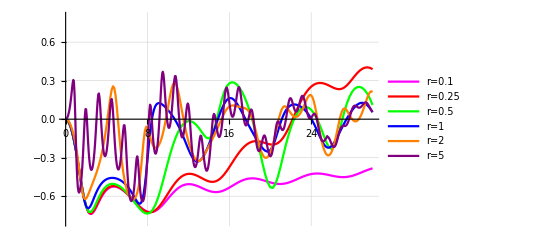

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kTr025[[All,1]],Re[v2kTr025[[All,2,1]]]}],Transpose[{v2kTr05[[All,1]],Re[v2kTr05[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}],Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=0.25","r=0.5","r=1","r=2","r=5"},Joined->{True,True,True,True,True,True}]}]
```

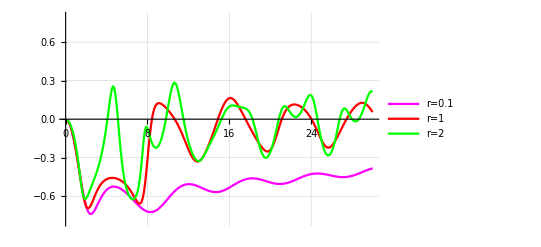

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}],Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}],Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}]},PlotRange->{{0,krange},{-0.8,0.8}},GridLines->Automatic,PlotStyle->{{Magenta},{Red},{Green},{Blue},{Orange},{Purple}},PlotLegends->{"r=0.1","r=1","r=2"},Joined->{True,True,True,True,True,True}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/ppv2

```mathematica
Export["v2kTr01.dat",Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}] ]
Export["v2kTr2.dat",Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}] ]
Export["v2kT.dat",Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]]
```

v2kTr01.dat

v2kTr2.dat

v2kT.dat

```mathematica
Export["v2kTr5.dat",Transpose[{v2kTr5[[All,1]],Re[v2kTr5[[All,2,1]]]}] ]
```

v2kTr5.dat